Derived from “BMAG toy model.nb”

Beware: Don’t trust “k” to relate to any typical terms. It’s just a generic free variable in this notebook

```mathematica
magnetEffect[vec_,k1_,k2_]:=(
{
vec[[1]],
vec[[2]]+vec[[1]]*k1+vec[[1]]^3*k2
}
)

driftEffect[vec_,d_]:=(
{
vec[[1]]+d*vec[[2]],
vec[[2]]
}

)
```

```mathematica
popCount=10000;
population=Transpose[{
RandomVariate[NormalDistribution[0,1],popCount],
RandomVariate[NormalDistribution[0,1],popCount]
}];
```

```mathematica
population = RandomVariate[UniformDistribution[{-3,3}],{popCount,2}];
population=Select[population,Norm[#]<3&];
```

```mathematica
fodoOnParticle[vec_,k1_,k2_,d_]:=(
magnetEffect[
driftEffect[
magnetEffect[
driftEffect[
vec,
d
],
k1,
k2
],
d
],
-k1,
-k2
]
)

fodoOnArray[arr_,k1_,k2_,d_]:=(fodoOnParticle[#,k1,k2,d]&/@arr)
```

```mathematica
nestList=NestList[
fodoOnArray[#,-0.871,-0.0015,1]&,
{{1,0.6},{0,1}}.#&/@population,
100
][[1;;-1;;5]];

imgArr=ListPlot[#,PlotRange->{{-10,10},{-10,10}},AspectRatio->1]&/@nestList;

(*binSize=0.25;
imgArr=DensityHistogram[#,{{binSize},{binSize}},PlotRange->{{-10,10},{-10,10}},ColorFunction->"Rainbow"]&/@nestList;*)

ListAnimate[imgArr]
```

```mathematica
emittance[pop_]:=√(Mean[(#[[1]])^2&/@pop]*Mean[(#[[2]])^2&/@pop]-Mean[#[[1]]*#[[2]]&/@pop]^2)
```

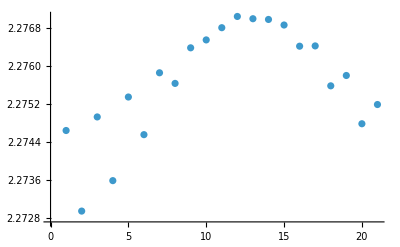

```mathematica
ListPlot[
emittance[#]&/@nestList
]
```

```mathematica
Sqrt[2]//N
```

1.41421